```mathematica
Needs["ErrorBarPlots`"];
```

```mathematica
Data1=Import["D:/Temp/Erf-fit1.txt","Table"];
Data2=Import["D:/Temp/Erf-fit2.txt","Table"];
Data3=Import["D:/Temp/PolarAngle.txt","Table"];
```

```mathematica
S3=(Part[Data1,All,2]-Part[Data2,All,2])/(Part[Data1,All,2]+Part[Data2,All,2]);
PolarAngle=π/2-ArcCos[S3];
AngleData=Transpose[{Part[Data1,All,1],PolarAngle}];
AngleData=Drop[AngleData,28];
ExpName="D:/Temp/PolarAngleFit.txt";
Export[ExpName,SetPrecision[AngleData,6],"Table"]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

D:/Temp/PolarAngleFit.txt

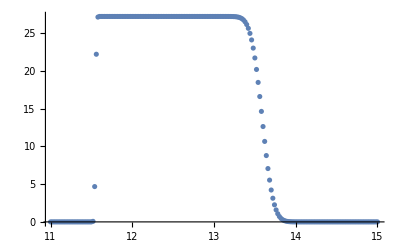

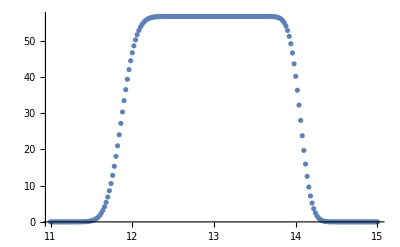

```mathematica
ListPlot[Data1]
ListPlot[Data2]
```

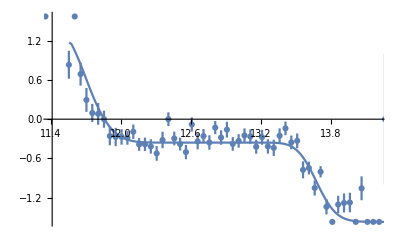

```mathematica
FitPlot=ListPlot[AngleData,PlotRange->{{12,14},Automatic},Joined->True];
XCol=1;YCol=2;YErrCol=3;
DataAndErr[TheTab_]:=Table[{{Part[TheTab,Ind,XCol],Part[TheTab,Ind,YCol]},ErrorBar[Part[TheTab,Ind,YErrCol]]},{Ind,Length[TheTab]}];
DataPlot=ErrorListPlot[DataAndErr[Data3],PlotRange->{{11.4,14.2},Automatic}];
Show[DataPlot,FitPlot]
```